```mathematica
Clear["Global`*"]
(*Data import*)
SetDirectory[NotebookDirectory[]];
dataI=Import["CSV\\time_series_covid_19_confirmed.csv","Data"];
dataD=Import["CSV\\time_series_covid_19_deaths.csv","Data"];
dataR=Import["CSV\\time_series_covid_19_recovered.csv","Data"];
dataPop=Import["CSV\\population.csv ","Data"];
(*Returns a population of a country.country is a string,for←-example," China "*)
population[country_]:=Module[{pos}, 
pos=Position[dataPop[[All,1]],country][[1,1]]; 
dataPop[[pos,2]] ]

(*Small tricks for ticks*)
 dates=dataI[[1,5;;]];
 datesTicks=Transpose[{Range[Length[dates]],dates}];
(*Returns a List of cases according to the dates.*)
CasesPerCountry[data_,country_]:=Module[
{countryData,pos}, countryData=data[[2;; ,2]];
pos=Flatten@Position[countryData,country];
Plus@@data[[pos+1]][[All,5;;]]
 ]
 IList=CasesPerCountry[dataI,"Belarus"]//N;
 RList=CasesPerCountry[dataR,"Belarus"]//N;
DList= CasesPerCountry[dataD,"Belarus"]//N;
Nt=population["Belarus"];
Time=83-38+5;
syst = {
s'[t]==-beta*k*s[t]*i[t]+gamma*r[t],
p'[t]==beta*k*s[t]*i[t]-beta*k*s[t-tau]*i[t-tau],
i'[t]==beta*k*s[t-tau]*i[t-tau]-(mu+d)*i[t],
r'[t]==mu*i[t]-gamma*r[t], 
r[t/;t<=0]==0,
i[t/;t<=0]==i0,
p[t/;t<=0]==k*i[0],
s[t/;t<=0]==1-p[0]-i[0]
};
solS=ParametricNDSolveValue[syst, s, {t,0,Time},{beta, mu, i0, d, gamma,k,tau}];
solI=ParametricNDSolveValue[syst, i, {t,0,Time},{beta, mu, i0, d, gamma,k,tau}]
solR=ParametricNDSolveValue[syst, r, {t,0,Time},{beta, mu, i0, d, gamma,k,tau}]
solE=ParametricNDSolveValue[syst, p, {t,0,Time},{beta, mu, i0, d, gamma,k,tau}];

IListT=Table[{i,IList[[i+38]]},{i,0,Length[IList]-38}]
RListT=Table[{i,RList[[i+38]]},{i,0,Length[RList]-38}]
Length[IList]
Length[RList]
plotCases[data_,country_,legend_]:= ListPlot[Table[ CasesPerCountry[data[[k]],country],{k,1,Length[data]}],FrameTicks->{datesTicks[[1;; ;;14]],Automatic}, FrameLabel->{"Date","People"},PlotLabel->country, PlotTheme->"Scientific",PlotLegends->legend,PlotRange->All,GridLines->Automatic]
(*Call of plotCases[]*)
```

ParametricFunction[<>]

ParametricFunction[<>]

{{0,1.},{1,1.},{2,1.},{3,1.},{4,1.},{5,6.},{6,6.},{7,6.},{8,6.},{9,6.},{10,6.},{11,9.},{12,9.},{13,12.},{14,27.},{15,27.},{16,27.},{17,36.},{18,36.},{19,51.},{20,51.},{21,69.},{22,76.},{23,76.},{24,81.},{25,81.},{26,86.},{27,86.},{28,94.},{29,94.},{30,94.},{31,152.},{32,152.},{33,163.},{34,304.},{35,351.},{36,440.},{37,562.},{38,700.},{39,861.},{40,1066.},{41,1486.},{42,1981.},{43,2226.},{44,2578.},{45,2919.},{46,3281.},{47,3728.},{48,4204.},{49,4779.}}

{{0,0.},{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.},{8,0.},{9,0.},{10,1.},{11,3.},{12,3.},{13,3.},{14,3.},{15,3.},{16,3.},{17,3.},{18,3.},{19,5.},{20,5.},{21,5.},{22,15.},{23,15.},{24,15.},{25,22.},{26,29.},{27,29.},{28,32.},{29,32.},{30,32.},{31,32.},{32,47.},{33,53.},{34,53.},{35,53.},{36,53.},{37,52.},{38,53.},{39,54.},{40,77.},{41,139.},{42,169.},{43,172.},{44,203.},{45,203.},{46,203.},{47,203.},{48,203.},{49,342.}}

87

87

```mathematica
ifit=FindFit[IListT,Nt*solI[beta, mu, i0, d, gamma,k,tau][t],{{beta,0.2}, {mu,0.0174},{i0,1/Nt},{d,0.00034},{gamma,0.107},{k,1.62},{tau,3}},t,Method->{NMinimize,Method->{"DifferentialEvolution"}}]
(*rfit=Quiet@FindFit[RListT,Nt*solI[beta, mu, i0, d, gamma,k,tau][t],{{gamma,0.107},{k,1.62}},t,Method->{NMinimize,Method->{"DifferentialEvolution"}}]*)
```

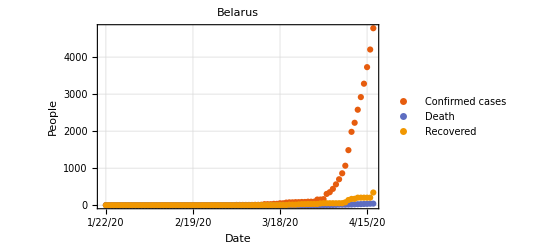

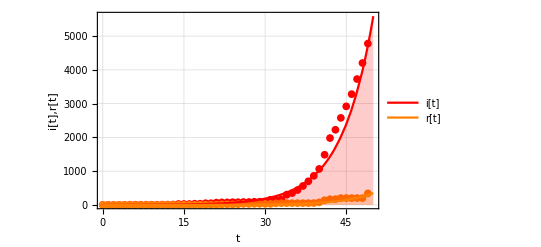

```mathematica
plotCases[{dataI,dataD,dataR},"Belarus",{"Confirmed cases", "Death","Recovered"}]
Show[ListPlot[{IListT,RListT},PlotRange->All,PlotStyle->{Red,Orange}],
Plot[{Nt*solI[0.191945, 0.0174, 1/Nt, 0.00034, 0.107,1.62,2.96][t],Nt*solR[0.191945, 0.0174, 1/Nt, 0.00034, 0.107,1.62,2.96][t]},{t,0,50},PlotRange->All,PlotLegends->Placed[{
Style["i[t]",16,Black,FontFamily->"Cambria"],
Style["r[t]",16,Black,FontFamily->"Cambria"]},Right],PlotStyle->{Red,Orange},Filling->Bottom],
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{
Style["t",16,Black,FontFamily->"Cambria"],
Style["i[t],r[t]",16,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->All]
```

```mathematica
(*Task 1. SEIRS*)
Manipulate[
Row[{
Plot[{
Nt*solS[beta, mu, i0, d, gamma,k,tau][t],
Nt*solI[beta, mu, i0, d, gamma,k,tau][t],
Nt*solR[beta, mu, i0, d, gamma,k,tau][t],
Nt*solE[beta, mu, i0, d, gamma,k,tau][t]},{t,0,100},
PlotStyle->{Blue, Red,Orange,Green},
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{
Style["t",20,Black,FontFamily->"Cambria"],
Style["s[t],i[t],r[t]",20,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->Automatic,PlotLegends->Placed[{
Style["s[t]",20,Black,FontFamily->"Cambria"],
Style["i[t]",20,Black,FontFamily->"Cambria"],
Style["r[t]",20,Black,FontFamily->"Cambria"],
Style["e[t]",20,Black,FontFamily->"Cambria"]},Right],ImageSize->512],
Plot[{
Nt*solI[beta, mu, i0, d, gamma,k,tau][t],
Nt*solR[beta, mu, i0, d, gamma,k,tau][t]},

{t,0,Time},
PlotStyle->{Red,Orange},
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{
Style["t",16,Black,FontFamily->"Cambria"],
Style["i[t],r[t]",16,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->All,PlotLegends->Placed[{
Style["i[t]",16,Black,FontFamily->"Cambria"],
Style["r[t]",16,Black,FontFamily->"Cambria"]},Right],ImageSize->324]
}],
{{beta, 0.191945},0,.2}, 
{{mu,0.0174},0,.1}, 
{{gamma,2*10^-4},0,0.2},
{{d,5*10^-3},0,0.01},
{{k,6},0,10},
{{tau,5},0,10},
{{i0, 1.0544631258989958*^-7}, 0, 1000000/Nt}]

Manipulate[
Row[{
Column[{
Show[ParametricPlot[{solS[beta, mu, i0, d, gamma,k,tau][t],(D[solS[beta, mu, i0, d, gamma,k,tau][f],f])/.{f->t}},{t,0,Time},AspectRatio->1/2],
FrameStyle->Directive[Black,12],Frame->True, FrameLabel->{
Style["s",12,Black,FontFamily->"Cambria"],
Style["s'",12,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->All,ImageSize->512
],
Show[ParametricPlot[{solI[beta, mu, i0, d, gamma,k,tau][t],(D[solI[beta, mu, i0, d, gamma,k,tau][f],f])/.{f->t}},{t,0,Time},AspectRatio->1/2],
FrameStyle->Directive[Black,12],Frame->True, FrameLabel->{
Style["i",12,Black,FontFamily->"Cambria"],
Style["i'",12,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->All,ImageSize->512
],
Show[ParametricPlot[{solR[beta, mu, i0, d, gamma,k,tau][t],(D[solR[beta, mu, i0, d, gamma,k,tau][f],f])/.{f->t}},{t,0,Time},AspectRatio->1/2],
FrameStyle->Directive[Black,12],Frame->True, FrameLabel->{
Style["r",12,Black,FontFamily->"Cambria"],
Style["r'",12,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->All,ImageSize->512
]}
]}],
{{beta, 0.191945},0,.2}, 
{{mu,0.0174},0,.1}, 
{{gamma,2*10^-4},0,0.2},
{{d,5*10^-3},0,0.01},
{{k,6},0,10},
{{tau,5},0,10},
{{i0, 1.0544631258989958*^-7}, 0, 1000000/Nt}]
```